## CA Manipulation

```mathematica
initialValues=SparseArray[{{1,2}->1,{5,6}->1,{6,5}->1,{6,6}->1,{6,7}->1,{7,6}->1},{11,11}]; (* Define starting values and lattice size. *)
```

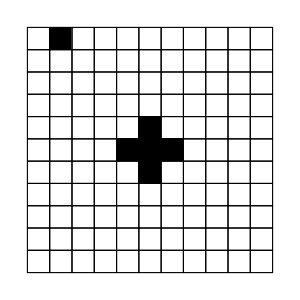

```mathematica
TessellationPlot[initialValues]
```

```mathematica
cellState[cell_,lattice_]:=lattice[[cell[[1]],cell[[2]]]]; (* Returns the value of the cell {x,y}. *)
```

```mathematica
Options[vonNeumannNeighborhood]={"CellShape"->Square};

vonNeumannNeighborhood[cell_,lattice_,OptionsPattern[vonNeumannNeighborhood]]:=
Module[
	{c1=cell[[1]],c2=cell[[2]],s=OptionValue["CellShape"]},
	Which[
		s===Square,
			{c1,c2}->{{c1-1,c2},{c1,c2-1},{c1,c2},{c1,c2+1},{c1+1,c2}},
			
		s===Hexagon,
			If[EvenQ[c1],
				{c1,c2}->{{c1-1,c2-1},{c1-1,c2},{c1,c2-1},{c1,c2},{c1,c2+1},{c1+1,c2-1},{c1+1,c2}},
				{c1,c2}->{{c1-1,c2},{c1-1,c2+1},{c1,c2-1},{c1,c2},{c1,c2+1},{c1+1,c2},{c1+1,c2+1}}
				],
			
		s===Triangle,
			If[EvenQ[c2],
				{c1,c2}->{{c1,c2-1},{c1,c2},{c1,c2+1},{c1+1,c2-1}},
				{c1,c2}->{{c1-1,c2+1},{c1,c2-1},{c1,c2},{c1,c2+1}}
				]
			]
]; (* Associates the cell to its von Neumann Neighborhood. *)
```

```mathematica
vonNeumannNeighborhood[{10,10},initialValues,"CellShape"->Square]
```

{10,10}→{{9,10},{10,9},{10,10},{10,11},{11,10}}

```mathematica
Options[vonNeumannNeighborhoodTable]:={"CellShape"->Square};

vonNeumannNeighborhoodTable[lattice_,OptionsPattern[vonNeumannNeighborhoodTable]]:=
Association[
	Flatten[
		Table[
			vonNeumannNeighborhood[
				{i,j},lattice,"CellShape"->OptionValue["CellShape"]
			],
			{i,1,Dimensions[lattice][[1]]},{j,1,Dimensions[lattice][[2]]}
		],1
	]
]; (* Associates all cells to their  von Neumann neighborhoods. *)
```

```mathematica
vonNeumannNeighborhoods=vonNeumannNeighborhoodTable[initialValues,"CellShape"->Square];
```

```mathematica
Options[neighborhoodState]:={"CellShape"->Square}

neighborhoodState[cell_,globalState_,OptionsPattern[neighborhoodState]]:=
Quiet[
	Module[
		{n=vonNeumannNeighborhoodTable[globalState,"CellShape"->OptionValue["CellShape"]]},
		Table[
			If[IntegerQ[cellState[n[[Key[cell]]][[i]],globalState]],
				cellState[n[[Key[cell]]][[i]],globalState],
				0
			],
		{i,1,Length[n[[Key[cell]]]]}
		]
	]
]; (* Returns the state of each cell in the von Neumann neighborhood of the specified cell. *)
```

```mathematica
neighborhoodState[{11,11},initialValues]
```

{0,0,0,0,0}

```mathematica
Options[cellEvolution]:={"CellShape"->Square};

cellEvolution[cell_,globalState_,rule_,OptionsPattern[cellEvolution]]:=
Lookup[
	rule,{{cellState[cell,globalState],Total[neighborhoodState[cell,globalState]]}}][[1]];(* Applies the specified evolution rule to the particular cell. *)
```

```mathematica
rules=<|{0,0}->0,{0,1}->1,{0,2}->0,{0,3}->1,{0,4}->0,{1,1}->0,{1,2}->1,{1,3}->0,{1,4}->1,{1,5}->0|>; (* An example set of rules. *)
cellEvolution[{9,11},initialValues,rules]
```

0

```mathematica
Options[globalEvolution]:={"CellShape"->Square};

globalEvolution[state_,func_Function,OptionsPattern[globalEvolution]]:=
Module[
	{rules=AssociationMap[
					func@@#&,
					Flatten[
						Table[
							{i-1,j-1},
							{i,1,2},
							{j,1,8}
							],
						1
					]
			]},
	SparseArray[
		{i_,j_}:>cellEvolution[{i,j},state,rules,"CellShape"->OptionValue["CellShape"]],
		Dimensions[state]
		]
]; (* Applies the specified rule to the current state. *)
```

```mathematica
Nest[globalEvolution[#,Mod[#1+#2,2]&,"CellShape"->Triangle]&,initialValues,4]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0)

## CA Graphics

#### 2D Graphics

```mathematica
hexagonCell[offset_:{0,0},basis_List:{{Sqrt[3]/2,1/2},{0,1}}]:=
	Module[
		{a=basis[[1]],b=basis[[2]]},
		Translate[Polygon[{{0,0},a-b,2*a-b,2*a,a+b,b}],offset]
	]; (* Plots a hexagonal cell with vertices belonging to the lattice and shifted by the offset vector. *)
```

```mathematica
Options[TessellationPlot]:={"CellShape"->Square,ImageSize->300}; (*Public*)

TessellationPlot[lattice_,basis_List:{{1,0},{0,1}},OptionsPattern[TessellationPlot]]:=
Graphics[
	Module[
		{b1=basis[[1]],b2={-basis[[2,1]],basis[[2,2]]},d1=Dimensions[lattice][[1]],d2=Dimensions[lattice][[2]],s=OptionValue["CellShape"]},
		Which[
			s===Square,
				Table[
					{FaceForm[GrayLevel[1-cellState[{i,j},lattice]]],
					EdgeForm[Black],
					Polygon[{b1*j-b2*i,b1*(j+1)-b2*i,b1*(j+1)-b2*(i+1),b1*j-b2*(i+1)}]},
				{i,1,d1},{j,1,d2}],
				
			s===Hexagon,
				Table[
					{FaceForm[GrayLevel[1-cellState[{i,j},lattice]]],
					EdgeForm[Black],
					hexagonCell[{i*(2*b1-b2)-If[EvenQ[j],3*j/2*{0,b2[[2]]},(3*j/2)*{0,b2[[2]]}+1/2{0,b2[[2]]-2b1[[2]]}]+If[EvenQ[j],0,{b1[[1]],0}]},basis]},
				{i,1,d1},{j,1,d2}],
				
			s===Triangle,
				Table[
					If[OddQ[j],
					
						{FaceForm[GrayLevel[1-cellState[{i,j},lattice]]],
						EdgeForm[Black],
						Triangle[{b1*((j-1)/2)-b2*(i-1),b1*((j+1)/2)-b2*(i-1),b1*(j-1)/2-b2*(i)}]},
						
						{FaceForm[GrayLevel[1-cellState[{i,j},lattice]]],
						EdgeForm[Black],
						Triangle[{b1*(j/2)-b2*(i-1),b1*(j/2-1)-b2*(i),b1*(j/2)-b2*(i)}]}],
				{i,1,d1},{j,1,d2}]
		]
	],
	ImageSize->OptionValue[ImageSize]
]; (* Plots the lattice with given state and cell shapes. *)
```

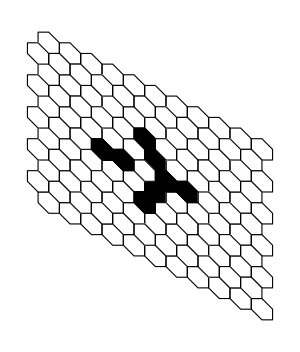

```mathematica
TessellationPlot[globalEvolution[initialValues,Mod[#1+#2,2]&],"CellShape"->Hexagon]
```

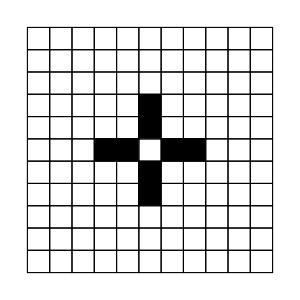

```mathematica
TessellationPlot[globalEvolution[initialValues,Mod[#1+#2,2]&],"CellShape"->Square]
```

```mathematica
Options[CAPlot]:={"CellShape"->Square};

CAPlot[lattice_,func_Function,time_Integer:0,basis_List:{{1,0},{0,1}},OptionsPattern[CAPlot]]:=
Module[
	{vNN=vonNeumannNeighborhoodTable[lattice,"CellShape"->OptionValue["CellShape"]],timestate=Nest[globalEvolution[#,func,"CellShape"->OptionValue["CellShape"]]&,lattice,time]},
	Graphics[
		(*ResourceFunction[*)TessellationPlot[
			timestate,
			basis,
			"CellShape"->OptionValue["CellShape"]
		]
	]
]; (* Plots the CA after applying the rule "func" to the initial lattice "times" times. *)
```

```mathematica
Options[CAEvolution]:={"CellShape"->Square};

CAEvolution[lattice_,func_Function,time_Integer:10,basis_List:{{1,0},{0,1}},OptionsPattern[CAEvolution]]:=
Module[
	{vNN=vonNeumannNeighborhoodTable[lattice,"CellShape"->OptionValue["CellShape"]],timestate=NestList[globalEvolution[#,func,"CellShape"->OptionValue["CellShape"]]&,lattice,time]},	
	Animate[
		TessellationPlot[
			timestate[[n]],
			basis,
			"CellShape"->OptionValue["CellShape"]
		],
	{{n,1},1,time,1},
	AnimationRate->2,
	AnimationRunning->False
	]
]; (* Animates the evolution of a CA. *)
```

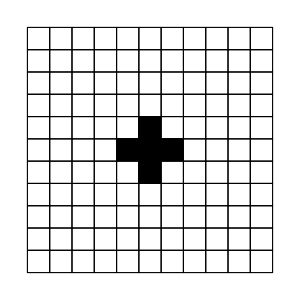
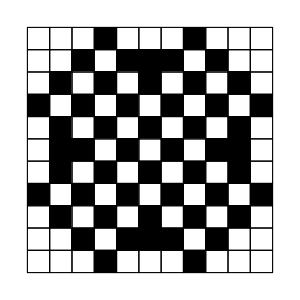
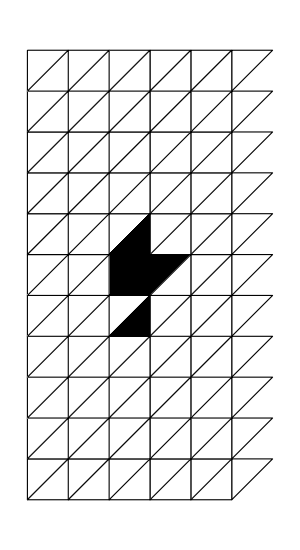
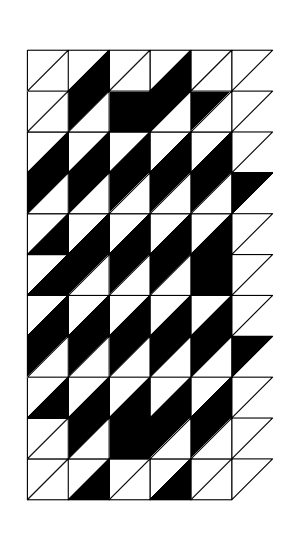
Game of Life, steps 1 and 15: | 
-Graphics- | -Graphics-
Triangular Game of Life, steps 1 and 15: | 
-Graphics- | -Graphics-

```mathematica
Grid[
{
{Style["Game of Life, steps 1 and 15:",FontWeight->Bold]},
{CAPlot[initialValues,Mod[#1+#2,2]&],CAPlot[initialValues,Mod[#1+#2,2]&,15]},
{Style["Triangular Game of Life, steps 1 and 15:",FontWeight->Bold]},
{CAPlot[initialValues,Mod[#1+#2,2]&,"CellShape"->Triangle],CAPlot[initialValues,Mod[#1+#2,2]&,15,"CellShape"->Triangle]}
},Frame->True
]
```

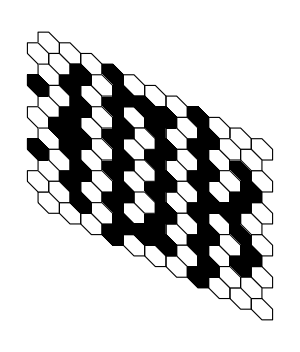

```mathematica
CAPlot[initialValues,Mod[#1+#2,2]&,15,"CellShape"->Hexagon]
```

```mathematica
CAEvolution[initialValues,Mod[#1+#2,2]&,20,"CellShape"->Hexagon]
```